```mathematica
FEt[pa_,pb_]:=Module[{n,n1,n2,ft,A,ev,i},n=40;
ft=0.0;
For[n1=0,n1<n,n1++,For[n2=0,n2<n,n2++,A={{-2 V pa,-1-Exp[I 2 Pi n2/n],-1-Exp[-I 2 Pi n1/n]},{-1-Exp[-I 2 Pi n2/n],-2 V pb,-1-Exp[-I 2 Pi n1/n] Exp[-I 2 Pi n2/n]},{-1-Exp[I 2 Pi n1/n],-1-Exp[I 2 Pi n1/n] Exp[I 2 Pi n2/n],2 V (pa+pb)}};
ev=Eigenvalues[A];
For[i=1,i<=3,i++,ft+=-T Log[1+Exp[-(ev[[i]]-mu)/T]]/n^2];];];
ft]
```

```mathematica
V=1.0;mu=0.1;T=0.2;
del=10^-6;mit=20;pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,
a[m]=pa;b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/6/V;
pb=(dfta-2 dftb)/6/V;]
```

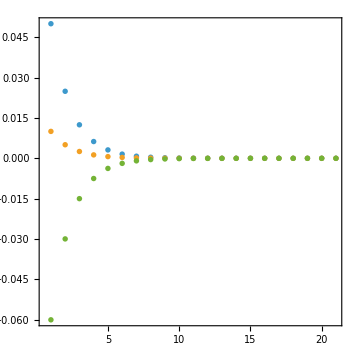

```mathematica
ListPlot[{Table[a[i],{i,0,mit}],Table[b[i],{i,0,mit}],Table[-a[i]-b[i],{i,0,mit}]},PlotRange->All,Joined->False,Frame->True,AspectRatio->1]
```

```mathematica
mu=-0.5;T=0.4;Vmin=1.5;Vmax=3.5;nV=100;
del=0.0000000001;mit=200;
For[iV=0,iV<=nV,iV++,
V=Vmin+iV/nV*(Vmax-Vmin);
pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/6/V;
pb=(dfta-2 dftb)/6/V;
];
dela[iV]=pa;
delb[iV]=pb;
delc[iV]=-pa-pb;
Print[iV/nV*100.]
]
```

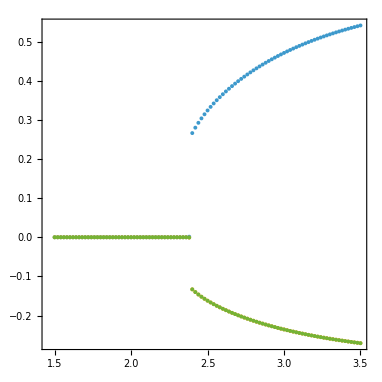

```mathematica
cha=Table[{Vmin+iV/nV*(Vmax-Vmin),dela[iV]},{iV,0,nV}];chb=Table[{Vmin+iV/nV*(Vmax-Vmin),delb[iV]},{iV,0,nV}];chc=Table[{Vmin+iV/nV*(Vmax-Vmin),delc[iV]},{iV,0,nV}];p1=ListPlot[{cha,chb,chc},Frame->True,PlotRange->All,AspectRatio->1]
```

```mathematica
Tmin=0.2;Tmax=1.5;Vmin=1.5;Vmax=3.5;ng=40;
For[i=0,i<=ng,i++,
For[j=0,j<=ng,j++,
V=Vmin+i/ng*(Vmax-Vmin);
T=Tmin+j/ng*(Tmax-Tmin);
del=0.0000000001;mit=20;pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,
a[m]=pa;b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/6/V;
pb=(dfta-2 dftb)/6/V;
];
If[Abs[a[20]]<Abs[a[5]],phase[i,j]=0,phase[i,j]=1]
];
Print[100.*i/ng]
]
```

0.

2.5

5.

7.5

10.

12.5

15.

17.5

20.

22.5

25.

27.5

30.

32.5

35.

37.5

40.

42.5

45.

47.5

50.

52.5

55.

57.5

60.

62.5

65.

67.5

70.

72.5

75.

77.5

80.

82.5

85.

87.5

90.

92.5

95.

97.5

100.

```mathematica
ListDensityPlot[Flatten[Table[{Vmin+i/ng*(Vmax-Vmin),Tmin+j/ng*(Tmax-Tmin),phase[i,j]},{i,0,ng},{j,0,ng}],1],InterpolationOrder->0]
```

-Graphics-

```mathematica
mu=-0.5;T=1.4;Vmin=2.0;Vmax=4.0;nb=10;
For[ib=1,ib<=nb,ib++,
V=(Vmin+Vmax)/2;
del=0.0000000001;mit=20;pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,
a[m]=pa;b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/6/V;
pb=(dfta-2 dftb)/6/V;
];
If[Abs[a[20]]<Abs[a[5]],Vmin=V,Vmax=V]
]
```

```mathematica
Vmin
```

3.5332

```mathematica
Vmax
```

3.53564

```mathematica
(* plotting T against V *)
mu=-0.5;Tmin=0.2;Tmax=1.4;nT=5;
For[iT=0,iT<=nT,iT++,
T=Tmin+iT/nT*(Tmax-Tmin);
Vmin=2.0;Vmax=4.0;nb=10;
For[ib=1,ib<=nb,ib++,
V=(Vmin+Vmax)/2;
del=0.0000000001;mit=20;pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,
a[m]=pa;b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/6/V;
pb=(dfta-2 dftb)/6/V;
];
If[Abs[a[60]]<Abs[a[5]],Vmin=V,Vmax=V]
];
x[iT]=T;
y[iT]=(Vmin+Vmax)/2
]
```

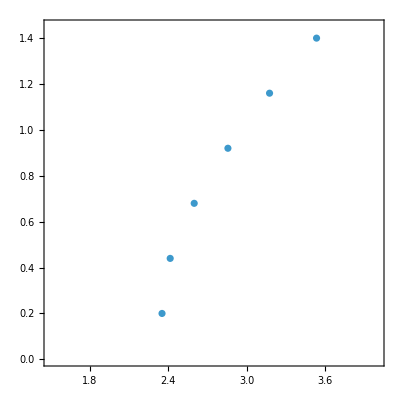

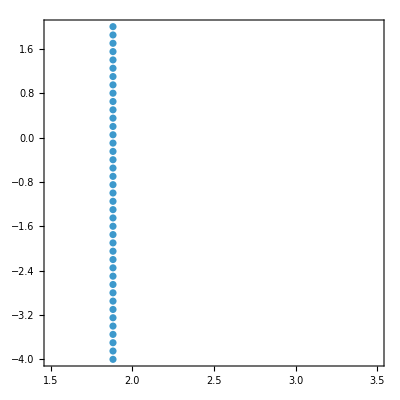

```mathematica
phase=Table[{y[iT],x[iT]},{iT,0,nT}];ListPlot[phase,AspectRatio->1,Frame->True,PlotRange->{{1.5,4.0},{0.0,1.45}}]
```

```mathematica
phase
```

{{1.88205,-4.},{1.88205,-3.85},{1.88205,-3.7},{1.88205,-3.55},{1.88205,-3.4},{1.88205,-3.25},{1.88205,-3.1},{1.88205,-2.95},{1.88205,-2.8},{1.88205,-2.65},{1.88205,-2.5},{1.88205,-2.35},{1.88205,-2.2},{1.88205,-2.05},{1.88205,-1.9},{1.88205,-1.75},{1.88205,-1.6},{1.88205,-1.45},{1.88205,-1.3},{1.88205,-1.15},{1.88205,-1.},{1.88205,-0.85},{1.88205,-0.7},{1.88205,-0.55},{1.88205,-0.4},{1.88205,-0.25},{1.88205,-0.1},{1.88205,0.05},{1.88205,0.2},{1.88205,0.35},{1.88205,0.5},{1.88205,0.65},{1.88205,0.8},{1.88205,0.95},{1.88205,1.1},{1.88205,1.25},{1.88205,1.4},{1.88205,1.55},{1.88205,1.7},{1.88205,1.85},{1.88205,2.}}

{{4.99805,-4.},{4.99805,-3.4},{4.99805,-2.8},{3.86523,-2.2},{3.11914,-1.6},{2.67773,-1.},{2.43945,-0.4},{2.35742,0.2},{2.43164,0.8},{2.70117,1.4},{3.27539,2.}}

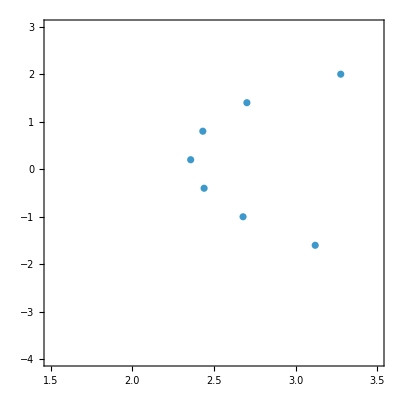

```mathematica
Mumin=-4.0;Mumax=2.0;nMu=10;
T=1.0 ;
For[iMu=0,iMu<=nMu,iMu++,Mu=Mumin+iMu/nMu*(Mumax-Mumin);
Vmin=1.0;Vmax=5.0;nb=10;
For[ib=1,ib<=nb,ib++,V=(Vmin+Vmax)/2;
del=10^-6;mit=20;pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
d = Sqrt[(pa-a[m])^2+(pb-b[m])^2];

If[d<10^-3,Vmin=V,Vmax=V];];
x[iMu]=Mu;
y[iMu]=(Vmin+Vmax)/2;]

phase=Table[{y[iMu],x[iMu]},{iMu,0,nMu}]

ListPlot[phase,AspectRatio->1,Frame->True,PlotRange->{{1.5,3.5},{-4.0,3.0}}]
(*okay now FEt is working for both! convergence condition instantly met for more runs so stops bisection, would have to make larger for more runs, could calculate rough estimate if had more time *)
```

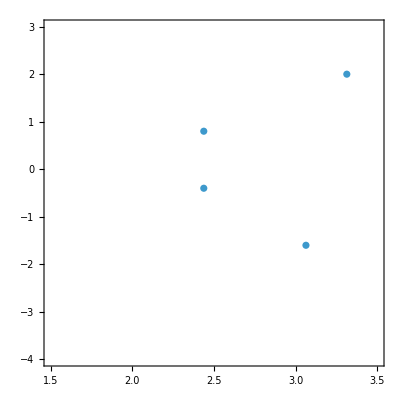

```mathematica
ListPlot[phase,AspectRatio->1,Frame->True,PlotRange->{{1.5,3.5},{-4.0,3.0}}]
```

```mathematica
Mumin=-4.0;Mumax=2.0;nMu=5;
T=1.0 ; Vplotmin=10;Vplotmax=5.0;
For[iMu=0,iMu<=nMu,iMu++,Mu=Mumin+iMu/nMu*(Mumax-Mumin);
Vmin=1.0;Vmax=5.0;nb=5;
For[ib=1,ib<=nb,ib++,V=(Vmin+Vmax)/2;
del=10^-6;mit=20;pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
d = Sqrt[(pa-a[mit])^2+(pb-b[mit])^2];

If[d<10^-3,Vmin=V,Vmax=V];];
Vc[iMu] = (Vmin+Vmax)/2;
muVal[iMu] = Mu ;
]

phasePlot1=Flatten[Table[{muVal[iMu],V,If[V>=Vc[iMu],1,0]
},{iMu,0,nMu},{j,0,nb}
],
1
];

Show[ListDensityPlot[phasePlot1,InterpolationOrder->0,ColorFunctionScaling->False,AspectRatio->1, ColorFunction->(If[#==1,Darker[Blue],Lighter[Yellow]]&),FrameLabel->{"V",Rotate["μ",-Pi/2]},Frame->True,PlotRange->{{1.0,5.0},{-4.0,3.0}}],ListLinePlot[]]
(* still issue with phase condition as not returning any less than that region, could just run V loop over that*)
```

-Graphics-

```mathematica
phasePlot1
```

{{-4.,10.,1},{-4.,9.5,1},{-4.,9.,1},{-4.,8.5,1},{-4.,8.,1},{-4.,7.5,1},{-4.,7.,1},{-4.,6.5,1},{-4.,6.,1},{-4.,5.5,1},{-4.,5.,1},{-3.4,10.,1},{-3.4,9.5,1},{-3.4,9.,1},{-3.4,8.5,1},{-3.4,8.,1},{-3.4,7.5,1},{-3.4,7.,1},{-3.4,6.5,1},{-3.4,6.,1},{-3.4,5.5,1},{-3.4,5.,1},{-2.8,10.,1},{-2.8,9.5,1},{-2.8,9.,1},{-2.8,8.5,1},{-2.8,8.,1},{-2.8,7.5,1},{-2.8,7.,1},{-2.8,6.5,1},{-2.8,6.,1},{-2.8,5.5,1},{-2.8,5.,1},{-2.2,10.,1},{-2.2,9.5,1},{-2.2,9.,1},{-2.2,8.5,1},{-2.2,8.,1},{-2.2,7.5,1},{-2.2,7.,1},{-2.2,6.5,1},{-2.2,6.,1},{-2.2,5.5,1},{-2.2,5.,1},{-1.6,10.,1},{-1.6,9.5,1},{-1.6,9.,1},{-1.6,8.5,1},{-1.6,8.,1},{-1.6,7.5,1},{-1.6,7.,1},{-1.6,6.5,1},{-1.6,6.,1},{-1.6,5.5,1},{-1.6,5.,1},{-1.,10.,1},{-1.,9.5,1},{-1.,9.,1},{-1.,8.5,1},{-1.,8.,1},{-1.,7.5,1},{-1.,7.,1},{-1.,6.5,1},{-1.,6.,1},{-1.,5.5,1},{-1.,5.,1},{-0.4,10.,1},{-0.4,9.5,1},{-0.4,9.,1},{-0.4,8.5,1},{-0.4,8.,1},{-0.4,7.5,1},{-0.4,7.,1},{-0.4,6.5,1},{-0.4,6.,1},{-0.4,5.5,1},{-0.4,5.,1},{0.2,10.,1},{0.2,9.5,1},{0.2,9.,1},{0.2,8.5,1},{0.2,8.,1},{0.2,7.5,1},{0.2,7.,1},{0.2,6.5,1},{0.2,6.,1},{0.2,5.5,1},{0.2,5.,1},{0.8,10.,1},{0.8,9.5,1},{0.8,9.,1},{0.8,8.5,1},{0.8,8.,1},{0.8,7.5,1},{0.8,7.,1},{0.8,6.5,1},{0.8,6.,1},{0.8,5.5,1},{0.8,5.,1},{1.4,10.,1},{1.4,9.5,1},{1.4,9.,1},{1.4,8.5,1},{1.4,8.,1},{1.4,7.5,1},{1.4,7.,1},{1.4,6.5,1},{1.4,6.,1},{1.4,5.5,1},{1.4,5.,1},{2.,10.,1},{2.,9.5,1},{2.,9.,1},{2.,8.5,1},{2.,8.,1},{2.,7.5,1},{2.,7.,1},{2.,6.5,1},{2.,6.,1},{2.,5.5,1},{2.,5.,1}}

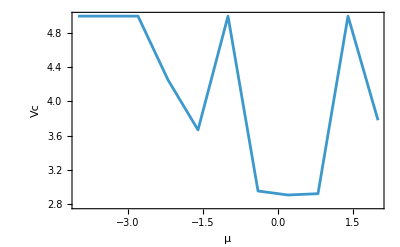

```mathematica
critLine=Table[{muVal[iMu],Vc[iMu]},{iMu,0,nMu}];
ListLinePlot[critLine,Frame->True,FrameLabel->{"μ","Vc"}]
```

```mathematica
phasePlot2=Flatten[Table[Vp=Vplotmin+j/nb (Vplotmax-Vplotmin);
{muVal[iMu],Vp,Boole[Vp>=Vc[iMu]]},{iMu,0,nMu},{j,0,nb}],1]
```

{{-4.,10.,1},{-4.,9.5,1},{-4.,9.,1},{-4.,8.5,1},{-4.,8.,1},{-4.,7.5,1},{-4.,7.,1},{-4.,6.5,1},{-4.,6.,1},{-4.,5.5,1},{-4.,5.,1},{-3.4,10.,1},{-3.4,9.5,1},{-3.4,9.,1},{-3.4,8.5,1},{-3.4,8.,1},{-3.4,7.5,1},{-3.4,7.,1},{-3.4,6.5,1},{-3.4,6.,1},{-3.4,5.5,1},{-3.4,5.,1},{-2.8,10.,1},{-2.8,9.5,1},{-2.8,9.,1},{-2.8,8.5,1},{-2.8,8.,1},{-2.8,7.5,1},{-2.8,7.,1},{-2.8,6.5,1},{-2.8,6.,1},{-2.8,5.5,1},{-2.8,5.,1},{-2.2,10.,1},{-2.2,9.5,1},{-2.2,9.,1},{-2.2,8.5,1},{-2.2,8.,1},{-2.2,7.5,1},{-2.2,7.,1},{-2.2,6.5,1},{-2.2,6.,1},{-2.2,5.5,1},{-2.2,5.,1},{-1.6,10.,1},{-1.6,9.5,1},{-1.6,9.,1},{-1.6,8.5,1},{-1.6,8.,1},{-1.6,7.5,1},{-1.6,7.,1},{-1.6,6.5,1},{-1.6,6.,1},{-1.6,5.5,1},{-1.6,5.,1},{-1.,10.,1},{-1.,9.5,1},{-1.,9.,1},{-1.,8.5,1},{-1.,8.,1},{-1.,7.5,1},{-1.,7.,1},{-1.,6.5,1},{-1.,6.,1},{-1.,5.5,1},{-1.,5.,1},{-0.4,10.,1},{-0.4,9.5,1},{-0.4,9.,1},{-0.4,8.5,1},{-0.4,8.,1},{-0.4,7.5,1},{-0.4,7.,1},{-0.4,6.5,1},{-0.4,6.,1},{-0.4,5.5,1},{-0.4,5.,1},{0.2,10.,1},{0.2,9.5,1},{0.2,9.,1},{0.2,8.5,1},{0.2,8.,1},{0.2,7.5,1},{0.2,7.,1},{0.2,6.5,1},{0.2,6.,1},{0.2,5.5,1},{0.2,5.,1},{0.8,10.,1},{0.8,9.5,1},{0.8,9.,1},{0.8,8.5,1},{0.8,8.,1},{0.8,7.5,1},{0.8,7.,1},{0.8,6.5,1},{0.8,6.,1},{0.8,5.5,1},{0.8,5.,1},{1.4,10.,1},{1.4,9.5,1},{1.4,9.,1},{1.4,8.5,1},{1.4,8.,1},{1.4,7.5,1},{1.4,7.,1},{1.4,6.5,1},{1.4,6.,1},{1.4,5.5,1},{1.4,5.,1},{2.,10.,1},{2.,9.5,1},{2.,9.,1},{2.,8.5,1},{2.,8.,1},{2.,7.5,1},{2.,7.,1},{2.,6.5,1},{2.,6.,1},{2.,5.5,1},{2.,5.,1}}

```mathematica
Mumin=-4.0;Mumax=2.0;nMu=40;
T=1.0;

VbisMin=1.0;VbisMax=5.0;nbis=10;
Vplotmin=1.5;Vplotmax=3.5;nV=40;

del=10^-6;mit=20;

(*---Step 1:find critical line Vc(mu) by bisection---*)
For[iMu=0,iMu<=nMu,iMu++,Mu=Mumin+iMu/nMu (Mumax-Mumin);
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
crit=If[Abs[a[mit]]<Abs[a[5]],0,1];
If[crit==1,v2=V,(*CDW side*)v1=V    (*disordered side*)];
];
muVal[iMu]=Mu;
Vc[iMu]=(v1+v2)/2;];

(*---Step 2:make explicit numeric arrays---*)
muVals=Table[muVal[i],{i,0,nMu}];
vcVals=Table[Vc[i],{i,0,nMu}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Optional check of the critical line---*)
critLine=Table[{muVals[[i+1]],vcVals[[i+1]]},{i,0,nMu}];

(*---Step 3:swap axes (V on x,mu on y)---*)phasePlot3=Flatten[Table[{vVals[[j+1]],(*x=V*)muVals[[i+1]],(*y=μ*)If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nMu},{j,0,nV}],1];

(*boundary also needs swapping*)
critLineSwapped=Table[{vcVals[[i+1]],muVals[[i+1]]},{i,0,nMu}];

ListDensityPlot[phasePlot3,InterpolationOrder->0,ColorFunctionScaling->False,(*swapped color scheme*)ColorFunction->(If[#==1,Lighter[Yellow,0.2],(*CDW*)Darker[Blue,0.7]       (*disordered*)]&),Frame->True,FrameLabel->{"V","μ"},LabelStyle->Directive[14],PlotRange->{{Vplotmin,Vplotmax},{Mumin,Mumax}},AspectRatio->1,(*nicer ticks*)FrameTicks->{Automatic,Automatic},(*cleaner boundary line*)Epilog->{Black,Thick,Line[critLineSwapped]}]
```

$Aborted

-Graphics-

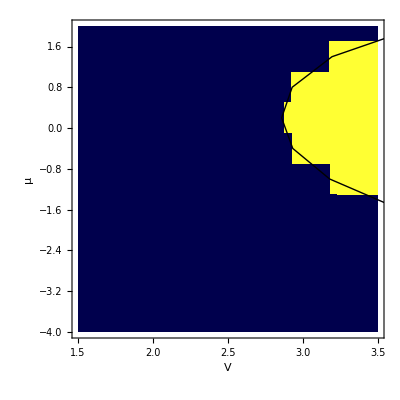

```mathematica
(*---Step 3:swap axes (V on x,mu on y)---*)phasePlot3=Flatten[Table[{vVals[[j+1]],(*x=V*)muVals[[i+1]],(*y=μ*)If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nMu},{j,0,nV}],1];

(*boundary also needs swapping*)
critLineSwapped=Table[{vcVals[[i+1]],muVals[[i+1]]},{i,0,nMu}];

ListDensityPlot[phasePlot3,InterpolationOrder->0,ColorFunctionScaling->False,(*swapped color scheme*)ColorFunction->(If[#==1,Lighter[Yellow,0.2],(*CDW*)Darker[Blue,0.7]       (*disordered*)]&),Frame->True,FrameLabel->{"V","μ"},LabelStyle->Directive[14],PlotRange->{{Vplotmin,Vplotmax},{Mumin,Mumax}},AspectRatio->1,(*nicer ticks*)FrameTicks->{Automatic,Automatic},(*cleaner boundary line*)Epilog->{Black,Thick,Line[critLineSwapped]}]
```

```mathematica
Mumin=-4.0;Mumax=2.0;nMu=60;
T=1.0;

VbisMin=1.0;VbisMax=6.0;nbis=18;
Vplotmin=2.0;Vplotmax=6.0;nV=120;

del=10^-6;mit=20;

(*---Step 1:critical line Vc(mu) by bisection---*)
For[iMu=0,iMu<=nMu,iMu++,Mu=Mumin+iMu/nMu (Mumax-Mumin);
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
crit=If[Abs[a[mit]]<Abs[a[5]],0,1];
If[crit==1,v2=V,(*CDW side*)v1=V    (*disordered side*)];];
muVal[iMu]=Mu;
Vc[iMu]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
muVals=Table[muVal[i],{i,0,nMu}];
vcVals=Table[Vc[i],{i,0,nMu}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with swapped axes:x=V,y=mu---*)
phasePlot=Flatten[Table[{vVals[[j+1]],muVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nMu},{j,0,nV}],1];

(*---Step 4:smooth boundary---*)
critLine=Table[{vcVals[[i+1]],muVals[[i+1]]},{i,0,nMu}];
smooth=Interpolation[critLine,InterpolationOrder->3];
muFine=Table[Mumin+t/400. (Mumax-Mumin),{t,0,400}];
smoothLine=Table[{smooth[mu],mu},{mu,muFine}];

ListDensityPlot[phasePlot,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],(*CDW*)RGBColor[0.10,0.15,0.55]    (*disordered*)]&),Frame->True,PlotLabel->T=1.0,FrameLabel->{Style["V",15],Style["μ",15]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Mumin,Mumax}},AspectRatio->1,ImageSize->500,Epilog->{Black,AbsoluteThickness[2.5],Line[smoothLine],Text[Style["CDW",16,Bold,Black],{4.9,0.3}],Text[Style["Disordered",16,Bold,White],{2.5,1.2}]}]
```

Interpolation::inddp: The point 5.99999 in dimension 1 is duplicated.

Set::write: Tag Rule in PlotLabel->1. is Protected.

ListDensityPlot::nonopt: Options expected (instead of 1.) beyond position 1 in ListDensityPlot[{{2.,-4.,0},{2.03333,-4.,0},{2.06667,-4.,0},{2.1,-4.,0},{2.13333,-4.,0},{2.16667,-4.,0},{2.2,-4.,0},<<38>>,{3.5,-4.,0},{3.53333,-4.,0},{3.56667,-4.,0},{3.6,-4.,0},{3.63333,-4.,0},<<7331>>},<<11>>,Epilog->{<<1>>}]. An option must be a rule or a list of rules.

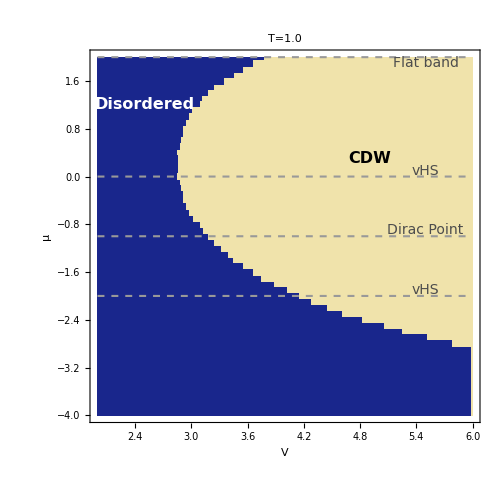

```mathematica
critLineMu=Table[{muVals[[i+1]],vcVals[[i+1]]},{i,0,nMu}];
smooth=Interpolation[critLineMu,InterpolationOrder->3];

muFine=Table[Mumin+t/400. (Mumax-Mumin),{t,0,400}];
smoothLine=Table[{smooth[mu],mu},{mu,muFine}];

ListDensityPlot[phasePlot,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],(*CDW*)RGBColor[0.10,0.15,0.55]    (*disordered*)]&),Frame->True,PlotLabel->"T=1.0",FrameLabel->{Style["V",15],Rotate[Style["μ",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Mumin,Mumax}},AspectRatio->1,ImageSize->500,Epilog->{Directive[GrayLevel[0.6],Dashed,AbsoluteThickness[1.5]],Line[{{Vplotmin,-1},{Vplotmax,-1}}],(*Dirac*)Line[{{Vplotmin,2},{Vplotmax,2}}],(*flat band*)Line[{{Vplotmin,0},{Vplotmax,0}}],(*van Hove*)Line[{{Vplotmin,-2},{Vplotmax,-2}}],(*van Hove*)Text[Style["Dirac Point",14,GrayLevel[0.3]],{5.5,-0.9}],Text[Style["Flat band",14,GrayLevel[0.3]],{5.5,1.9}],Text[Style["vHS",14,GrayLevel[0.3]],{5.5,0.1}],Text[Style["vHS",14,GrayLevel[0.3]],{5.5,-1.9}],Text[Style["CDW",16,Bold,Black],{4.9,0.3}],Text[Style["Disordered",16,Bold,White],{2.5,1.2}]}]
```

```mathematica
Mumin=-4.0;Mumax=2.0;nMu=60;
T=0.6;

VbisMin=1.0;VbisMax=6.0;nbis=18;
Vplotmin=2.0;Vplotmax=6.0;nV=120;

del=10^-6;mit=20;

(*---Step 1:critical line Vc(mu) by bisection---*)
For[iMu=0,iMu<=nMu,iMu++,Mu=Mumin+iMu/nMu (Mumax-Mumin);
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
crit=If[Abs[a[mit]]<Abs[a[5]],0,1];
If[crit==1,v2=V,(*CDW side*)v1=V    (*disordered side*)];];
muVal[iMu]=Mu;
Vc[iMu]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
muVals=Table[muVal[i],{i,0,nMu}];
vcVals=Table[Vc[i],{i,0,nMu}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with swapped axes:x=V,y=mu---*)
phasePlot4=Flatten[Table[{vVals[[j+1]],muVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nMu},{j,0,nV}],1];

critLineMu=Table[{muVals[[i+1]],vcVals[[i+1]]},{i,0,nMu}];
smooth=Interpolation[critLineMu,InterpolationOrder->3];

muFine=Table[Mumin+t/400. (Mumax-Mumin),{t,0,400}];
smoothLine=Table[{smooth[mu],mu},{mu,muFine}];

ListDensityPlot[phasePlot4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],(*CDW*)RGBColor[0.10,0.15,0.55]    (*disordered*)]&),Frame->True,PlotLabel->"T=0.6",FrameLabel->{Style["V",15],Rotate[Style["μ",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Mumin,Mumax}},AspectRatio->1,ImageSize->500,Epilog->{Directive[GrayLevel[0.6],Dashed,AbsoluteThickness[1.5]],Line[{{Vplotmin,-1},{Vplotmax,-1}}],(*Dirac*)Line[{{Vplotmin,2},{Vplotmax,2}}],(*flat band*)Line[{{Vplotmin,0},{Vplotmax,0}}],(*van Hove*)Line[{{Vplotmin,-2},{Vplotmax,-2}}],(*van Hove*)Text[Style["Dirac Point",14,GrayLevel[0.3]],{5.5,-0.9}],Text[Style["Flat band",14,GrayLevel[0.3]],{5.5,1.9}],Text[Style["vHS",14,GrayLevel[0.3]],{5.5,0.1}],Text[Style["vHS",14,GrayLevel[0.3]],{5.5,-1.9}],Text[Style["CDW",16,Bold,Black],{4.9,0.3}],Text[Style["Disordered",16,Bold,White],{2.5,1.2}]}]
```

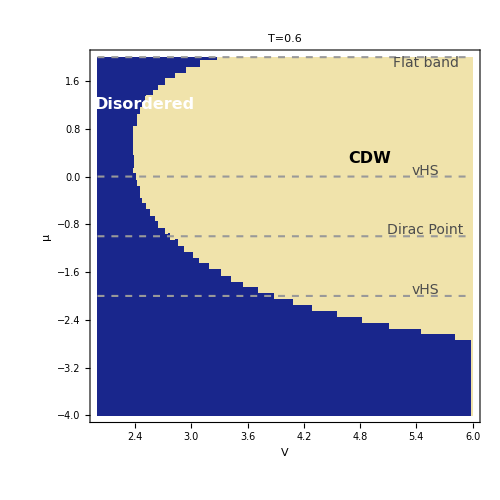

```mathematica
ListDensityPlot[phasePlot4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],(*CDW*)RGBColor[0.10,0.15,0.55]    (*disordered*)]&),Frame->True,PlotLabel->"T=0.6",FrameLabel->{Style["V",15],Rotate[Style["μ",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Mumin,Mumax}},AspectRatio->1,ImageSize->500,Epilog->{Directive[GrayLevel[0.6],Dashed,AbsoluteThickness[1.5]],Line[{{Vplotmin,-1},{Vplotmax,-1}}],(*Dirac*)Line[{{Vplotmin,2},{Vplotmax,2}}],(*flat band*)Line[{{Vplotmin,0},{Vplotmax,0}}],(*van Hove*)Line[{{Vplotmin,-2},{Vplotmax,-2}}],(*van Hove*)Text[Style["Dirac Point",14,GrayLevel[0.3]],{5.5,-0.9}],Text[Style["Flat band",14,GrayLevel[0.3]],{5.5,1.9}],Text[Style["vHS",14,GrayLevel[0.3]],{5.5,0.1}],Text[Style["vHS",14,GrayLevel[0.3]],{5.5,-1.9}],Text[Style["CDW",16,Bold,Black],{4.9,0.3}],Text[Style["Disordered",16,Bold,White],{2.5,1.2}]}]
(*put disordered lower down *)
```

```mathematica
muFixed=-0.5;

Tmin=0.1;Tmax=1.4;nT=65;

VbisMin=1.5;VbisMax=3.5;nbis=18;
Vplotmin=1.5;Vplotmax=3.5;nV=120;

del=10^-6;mit=40;
ordCut=10^-3;

(*---Step 1:critical line Vc(T) by bisection at fixed mu---*)
For[iT=0,iT<=nT,iT++,T=Tmin+iT/nT (Tmax-Tmin);
Mu=muFixed;
v1=VbisMin;
v2=VbisMax;
For[ib=1,ib<=nbis,ib++,V=(v1+v2)/2;
pa=0.05;
pb=0.01;
For[m=0,m<=mit,m++,a[m]=pa;
b[m]=pb;
dfta=(FEt[pa+del,pb]-FEt[pa,pb])/del;
dftb=(FEt[pa,pb+del]-FEt[pa,pb])/del;
pa=(dftb-2 dfta)/(6 V);
pb=(dfta-2 dftb)/(6 V);];
ord=Sqrt[pa^2+pb^2+(pa+pb)^2];
crit=If[ord>ordCut,1,0];
If[crit==1,v2=V,v1=V];];
tVal[iT]=T;
Vc[iT]=(v1+v2)/2;];

(*---Step 2:explicit arrays---*)
tVals=Table[tVal[i],{i,0,nT}];
vcVals=Table[Vc[i],{i,0,nT}];
vVals=Table[Vplotmin+j/nV (Vplotmax-Vplotmin),{j,0,nV}];

(*---Step 3:phase map with axes x=V,y=T---*)
phasePlotVT4=Flatten[Table[{vVals[[j+1]],tVals[[i+1]],If[vVals[[j+1]]>=vcVals[[i+1]],1,0]},{i,0,nT},{j,0,nV}],1];

critLineT=Table[{tVals[[i+1]],vcVals[[i+1]]},{i,0,nT}];
smooth=Interpolation[critLineT,InterpolationOrder->3];

tFine=Table[Tmin+s/400. (Tmax-Tmin),{s,0,400}];
smoothLine=Table[{smooth[t],t},{t,tFine}];

ListDensityPlot[phasePlotVT4,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(If[#==1,RGBColor[0.94,0.89,0.67],RGBColor[0.10,0.15,0.55]]&),Frame->True,PlotLabel->"μ = -4.0",FrameLabel->{Style["V",15],Rotate[Style["T",15],-Pi/2]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,12],PlotRange->{{Vplotmin,Vplotmax},{Tmin,Tmax}},AspectRatio->1,ImageSize->500,Epilog->{Text[Style["CDW",16,Bold,Black],{21.5,0.45}],Text[Style["Disordered",16,Bold,White],{17.5,1.15}]}],Graphics[{Black,Thick,Line[smoothLine]}]
```